# Ciclos en el método de Schröder aplicado a polinomios cúbicos (caso Lambda imaginario puro)

### La función de iteración para lambda=b*I

```mathematica
p[z_]=(z^2-1)(z-b*I); lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z]//Simplify//Together
```

(ⅈ b-4 b^2 z-10 ⅈ b z^2+4 z^3+ⅈ b z^4)/(1-2 b^2-4 ⅈ b z-2 b^2 z^2-4 ⅈ b z^3+3 z^4)

```mathematica
sp[I*y]//Factor
```

-(ⅈ (-b+4 b^2 y-10 b y^2+4 y^3-b y^4))/(1-2 b^2+4 b y+2 b^2 y^2-4 b y^3+3 y^4)

Podemos reducir el estudio a una función real de variable real (y) dependiente de un parámetro real (b).

```mathematica
rR[b_,y_]=-(-b+4 b^2 y-10 b y^2+4 y^3-b y^4)/(1-2 b^2+4 b y+2 b^2 y^2-4 b y^3+3 y^4);
```

```mathematica
D[rR[b,y],y]//Factor
```

(4 (b-y) (1+y^2) (-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3))/(1-2 b^2+4 b y+2 b^2 y^2-4 b y^3+3 y^4)^2

Dibujamos la función cúbica que nos da los punts crítocs libres

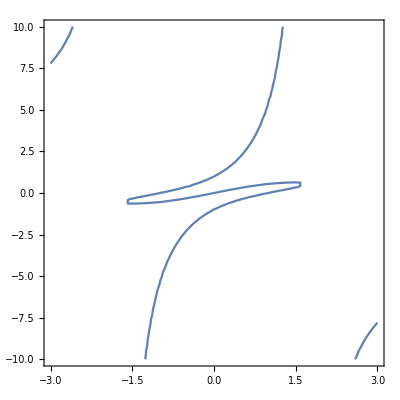

```mathematica
ContourPlot[-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3==0,{b,-3,3},{y,-10,10}]
```

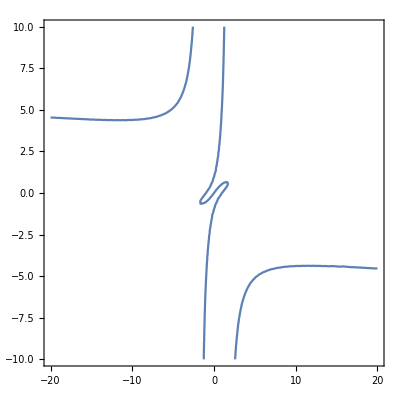

```mathematica
ContourPlot[-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3==0,{b,-20,20},{y,-10,10}]
```

Si b^2 < 3, existen tres puntos críticos libres. Si no, solo uno. El caso b = Sqrt[3] merece ser estudiado aparte. Como existe una simetría, podemos estudiar solo b>=0.

```mathematica
pp[b_,y_]=-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3;pp[-b,y]+pp[b,-y]
```

0

### Un casos particulares

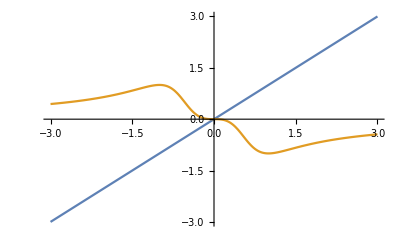

```mathematica
Plot[{y,rR[0,y]},{y,-3,3}]
```

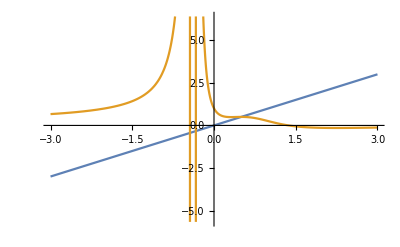

```mathematica
Plot[{y,rR[0.5,y]},{y,-3,3}]
```

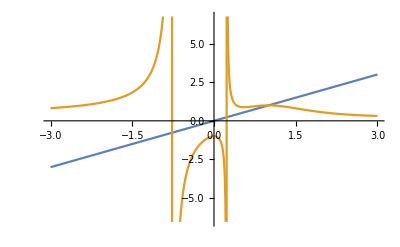

```mathematica
Plot[{y,rR[1.,y]},{y,-3,3}]
```

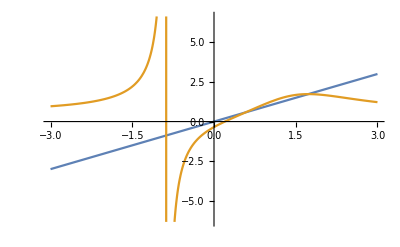

```mathematica
Plot[{y,rR[Sqrt[3.],y]},{y,-3,3}]
```

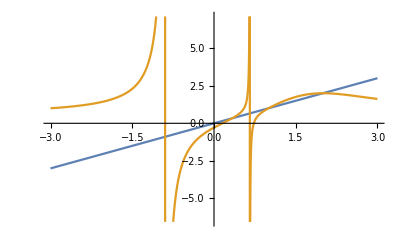

```mathematica
Plot[{y,rR[2.,y]},{y,-3,3}]
```

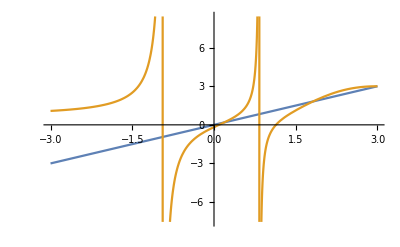

```mathematica
Plot[{y,rR[3.,y]},{y,-3,3}]
```

### Dos ciclos superatractores

Deben de ser soluciones de esta ecuación

```mathematica
rR[b,rR[b,y]]-y//Together//Factor
```

-(((b-y) (-1+2 b y-3 y^2) (1+y^2) (1-3 b^2+8 b y-3 y^2+b^2 y^2) (-1+3 b^2-8 b^4+16 b^6-10 b y+54 b^3 y-136 b^5 y+y^2-111 b^2 y^2+460 b^4 y^2-32 b^6 y^2+72 b y^3-744 b^3 y^3+176 b^5 y^3-22 y^4+574 b^2 y^4-340 b^4 y^4+16 b^6 y^4-212 b y^5+276 b^3 y^5-72 b^5 y^5+22 y^6-110 b^2 y^6+148 b^4 y^6+24 b y^7-200 b^3 y^7-9 y^8+159 b^2 y^8-4 b^4 y^8-66 b y^9+6 b^3 y^9+9 y^10-3 b^2 y^10))/(-1+6 b^2-17 b^4+32 b^6-56 b^8+32 b^10-16 b y+96 b^3 y-272 b^5 y+576 b^7 y-320 b^9 y-144 b^2 y^2+816 b^4 y^2-2416 b^6 y^2+1360 b^8 y^2-256 b^10 y^2+32 b y^3-992 b^3 y^3+5152 b^5 y^3-2912 b^7 y^3+2944 b^9 y^3-12 y^4+440 b^2 y^4-5796 b^4 y^4+2432 b^6 y^4-15384 b^8 y^4+448 b^10 y^4-144 b y^5+3520 b^3 y^5+1904 b^5 y^5+48160 b^7 y^5-4608 b^9 y^5-1424 b^2 y^6-5504 b^4 y^6-99920 b^6 y^6+20768 b^8 y^6-256 b^10 y^6+288 b y^7+4032 b^3 y^7+142432 b^5 y^7-53440 b^7 y^7+2176 b^9 y^7-54 y^8-1356 b^2 y^8-138894 b^4 y^8+85664 b^6 y^8-7976 b^8 y^8+32 b^10 y^8+80 b y^9+89824 b^3 y^9-87600 b^5 y^9+16768 b^7 y^9-192 b^9 y^9-36784 b^2 y^10+56496 b^4 y^10-23056 b^6 y^10+528 b^8 y^10+8544 b y^11-22112 b^3 y^11+22880 b^5 y^11-992 b^7 y^11-876 y^12+4696 b^2 y^12-17460 b^4 y^12+1472 b^6 y^12-8 b^8 y^12-432 b y^13+9984 b^3 y^13-1584 b^5 y^13+32 b^7 y^13-3888 b^2 y^14+1056 b^4 y^14-48 b^6 y^14+864 b y^15-384 b^3 y^15+32 b^5 y^15-81 y^16+54 b^2 y^16-9 b^4 y^16))

Que a su vez sean soluciones de la ecuación de puntos críticos libres. Hay tres posibilidades

```mathematica
NSolve[{-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3==0,-1+2 b y-3 y^2==0},{b,y},Reals]
```

{{b→-1.73205,y→-0.57735},{b→-1.73205,y→-0.57735},{b→1.73205,y→0.57735},{b→1.73205,y→0.57735}}

```mathematica
NSolve[{-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3==0,1-3 b^2+8 b y-3 y^2+b^2 y^2==0},{b,y},Reals]
```

{{b→-1.73205,y→-0.57735},{b→1.73205,y→0.57735}}

```mathematica
NSolve[{-2 b+2 b^3+3 y-9 b^2 y+12 b y^2-3 y^3+b^2 y^3==0,-1+3 b^2-8 b^4+16 b^6-10 b y+54 b^3 y-136 b^5 y+y^2-111 b^2 y^2+460 b^4 y^2-32 b^6 y^2+72 b y^3-744 b^3 y^3+176 b^5 y^3-22 y^4+574 b^2 y^4-340 b^4 y^4+16 b^6 y^4-212 b y^5+276 b^3 y^5-72 b^5 y^5+22 y^6-110 b^2 y^6+148 b^4 y^6+24 b y^7-200 b^3 y^7-9 y^8+159 b^2 y^8-4 b^4 y^8-66 b y^9+6 b^3 y^9+9 y^10-3 b^2 y^10==0},{b,y},Reals]
```

{{b→0,y→-1.},{b→0,y→1.}}

Solo salen los casos b=0 y b = Sqrt[3]